John Arban Lewis III SID 904082686 johnlewis1928@gmail.com HW 5

Problem 1 Done

A)

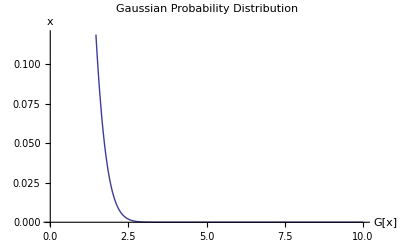

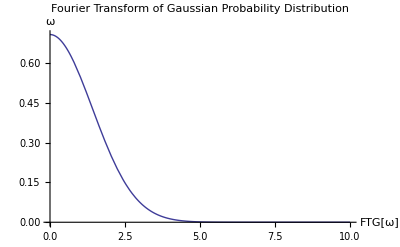

```mathematica
Remove["Global`*"]
G[x_]=M Exp[-α x^2];
FTG[ω_]=FourierTransform[G[x],x,ω];
(**********Parameter Block***************)
M=1;α=1;
(***************************************)
Plot[G[x],{x,0,10},PlotLabel->"Gaussian Probability Distribution",AxesLabel->{"G[x]","x"}]
Plot[FTG[ω],{ω,0,10},PlotLabel->"Fourier Transform of Gaussian Probability Distribution",AxesLabel->{"FTG[ω]","ω"}]
```

B) Done

```mathematica
Remove["Global`*"]
b[x_,Δx_]=f[x_]=HeavisideTheta[-Abs[x]+Δx];
Manipulate[Plot[b[x,Δx],{x,-10,10},PlotRange->All,PlotLabel->"Box Function",Exclusions->None],{{Δx,1},0,10}]
FTf[ω_,Δx_]=FourierTransform[f[x],x,ω];
Manipulate[Plot[FTf[ω,Δx],{ω,0,10},PlotRange->Full,Axes->True,PlotStyle->{Thick,Red},AxesLabel->{"ω","Fourier Transform"},PlotLabel->"Fourier Transform of Box Function",Exclusions->None],{{Δx,1},0,10}]
P[ω_,Δx_]=FTf[ω,Δx] FTf[ω,Δx]* /.Conjugate[HeavisideTheta[Δx]]-> HeavisideTheta[Δx]/.Conjugate[Δx ω]->Δx ω/.Conjugate[ω]->ω //ExpToTrig //Simplify;
Z[Δx_]=Integrate[P[ω,Δx],{ω,-Infinity,Infinity},Assumptions->{Δx∈Reals}];
Plot3D[(P[ω,Δx])/Z[Δx],{ω,1,2 Pi},{Δx,1,10},PlotRange->Full,Axes->True,AxesLabel->{"ω","Δx","Prabability"},PlotLabel->"3D Plot of Probability Density Function wrt ω and Δx",PlotPoints->30,MaxRecursion->15,Mesh->None,ColorFunction->"CMYKColors",Exclusions->None]
Print["In quantum mechanics ω is related to the Momentum of a particle E=ℏω -> p=√(2 ℏ ω m). 
As we know Δx Δp >= ℏ/2 according to the Heisenberg Uncertainty Principle.  The Graph of Shows us the Spread of values the momentum can take. "]
```

-Graphics3D-

In quantum mechanics ω is related to the Momentum of a particle E=ℏω -> p=√(2 ℏ ω m). 
As we know Δx Δp >= ℏ/2 according to the Heisenberg Uncertainty Principle.  The Graph of Shows us the Spread of values the momentum can take.

Problem 2 Done

```mathematica
Remove["Global`*"]
T=1/2 m (x1'[t]^2 + y1'[t]^2 + x2'[t]^2 + y2'[t]^2);
V=m g(y1[t] + y2[t]);
lag=T-V ;
EL[f_,q_]:=D[f,q]-Dt[D[f,D[q,t]],t,Constants->clist]
x1[t_]=l Sin[θ[t]];
x2[t_]=l Sin[θ[t]]+l Sin[ϕ[t]];
y1[t_]=-l Cos[θ[t]];
y2[t_]=-l Cos[θ[t]] -l Cos[ϕ[t]];
clist={l,m,g};
lag//FullSimplify
EL[lag,θ[t]] //FullSimplify
EL[lag,ϕ[t]] //FullSimplify
```

1/2 l m (2 g (2 Cos[θ[t]]+Cos[ϕ[t]])+l (2 θ'[t]^2+2 Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+ϕ'[t]^2))

-l m (2 g Sin[θ[t]]+l Sin[θ[t]-ϕ[t]] ϕ'[t]^2+2 l θ''[t]+l Cos[θ[t]-ϕ[t]] ϕ''[t])

-l m (g Sin[ϕ[t]]+l (-Sin[θ[t]-ϕ[t]] θ'[t]^2+Cos[θ[t]-ϕ[t]] θ''[t]+ϕ''[t]))

Problem 3 Done

```mathematica
Remove["Global`*"]
T=1/2 m (x1'[t]^2 + y1'[t]^2) +1/2 m( x2'[t]^2 + y2'[t]^2);
V=m g (y1[t] +y2[t]);
lag=T-V ;
clist={l,m,g};
EL[f_,q_]:=D[f,q]-Dt[D[f,D[q,t]],t,Constants->clist];
x1[t_]=l Sin[θ1[t]];
x2[t_]=l Sin[θ1[t]]+l Sin[θ2[t]];
y1[t_]=-l Cos[θ1[t]];
y2[t_]=-l Cos[θ1[t]]-l Cos[θ2[t]];
osc1[t_]=EL[lag,θ1[t]] //FullSimplify
osc2[t_]=EL[lag,θ2[t]] //FullSimplify
(************Parameter Block*****************)
m=1;tmin=0;tmax=20;tstep=.0001;g=10;l=1;
(********************************************)
soln=NDSolve[{osc1[t]==0,θ1[0]==π/6,θ1'[0]==0,osc2[t]==0,θ2[0]==0,θ2'[0]==0},{θ1,θ2},{t,tmin,tmax},MaxSteps->Infinity][[1]];

θ1[t_]=θ1[t]/.soln
θ2[t_]=θ2[t]/.soln

Animate[
{
	{
	Plot[{θ1[t],θ2[t]},{t,tmin,c},PlotRange->All,ImageSize->Medium],
	ListLinePlot[{{0,0},{x1[c],y1[c]},{x2[c],y2[c]}},PlotRange->{{-2,2},{0,-2}},PlotMarkers->Automatic,PlotStyle->{Blue,PointSize[.03]},ImageSize->Medium,PlotLabel->"The Double Pendulum--Pretty Awesome??"]
},

	{
	ParametricPlot[{{Evaluate[x1[t]/.soln],Evaluate[y1[t]/.soln]},{Evaluate[x2[t]/.soln],Evaluate[y2[t]/.soln]}},{t,tmin,c},PlotRange->{{-1,1},{0,-2.2}},ImageSize->Medium,PlotLabel->"Double Pendulum Path"],

	ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.soln],{t,tmin,c},ImageSize->Medium,AxesLabel->{"θ1","θ2"},PlotLabel->"Lissajous Curves",PlotRange->{{-.7,.7},{-1,1}}]
	}
}//MatrixForm
,{{c,"time",tmax},tmin+tstep,tmax,tstep},AnimationRate->.3,AnimationRunning->True]
```

-l m (2 g Sin[θ1[t]]+l Sin[θ1[t]-θ2[t]] θ2'[t]^2+2 l θ1''[t]+l Cos[θ1[t]-θ2[t]] θ2''[t])

-l m (g Sin[θ2[t]]+l (-Sin[θ1[t]-θ2[t]] θ1'[t]^2+Cos[θ1[t]-θ2[t]] θ1''[t]+θ2''[t]))

InterpolatingFunction[{{0.,20.}},<>][t]

InterpolatingFunction[{{0.,20.}},<>][t]

Problem 4

```mathematica
Remove["Global`*"]
T=1/2 m (x'[t]^2 + y'[t]^2);
V=-4 π^2/r^(1+ϵ);
L=T-V;
r=√(x[t]^2+ y[t]^2);
clist={m,ϵ};
el[f_,q_]:=D[f,q]-Dt[D[f,D[q,t]],t,Constants->clist];
elx[t_,ϵ_]=el[L,x[t]];
ely[t_,ϵ_]=el[L,y[t]];
m=1;thi=10;tlo=0;
soln[ϵ_]:=NDSolve[{elx[t,ϵ]==0,x[0]==1,x'[0]==-π,ely[t,ϵ]==0,y[0]==0,y'[0]==2 π},{x,y},{t,-thi,thi},MaxSteps->Infinity][[1]]
Manipulate[ParametricPlot[Evaluate[{x[t]/.soln[ϵ],y[t]/.soln[ϵ]}],{t,-thi,thi},PlotRange->{{-3,3},{-3,3}}],{{ϵ,0},-.855,.855}]
```